# Evaluation of Histogram Probability Model

## Eric Moyer

June 2013

## Introduction

I want to model probability densities for functions with bounded support. The most obvious way to do this is to create a histogram with a grid dependent on the number of samples I've seen - put the boundaries half-way between each sample.

A refinement is to start a histogram with a single uniform bin and split it when each data point is seen, giving equal probability to the two bins so formed. Given such a set of models, what is the posterior probability density over them after the data has been seen?

One can then go farther and look at 3 bin histograms after two data points have been seen. Can the 3 bin histogram be arrived at from splitting the 2 bin histogram? I imagine it can.

## Why I didn't finish

I realized that using the posterior distribution for the histogram bin boundary would be intractible even if I could calculate the posterior tractably.

The application I am concerned about right now is sampling from an unknown distribution then using that sample to construct a set of equiprobable bins which I will then use to bin another distribution. The KL divergence between the distribution of the bins from the unknown distribution and the other distribution will be the error in the other distribution's approximation of the unknown distribution. However, to use the histogram bin posterior, I'd have to re-bin the other distribution according to all binnings and assign that binning a probability according to the posterior. But that "re-bin according to all possible sets of histograms" step is intractable unless a simplification falls out of the math. Thus, even if I can calculate the probability model, it is in vain. So, I'm giving up now and am going to spend my time on more profitable things.

## Two bin histogram on [0..1]

### Likelihood and joint distribution

If we have n hypotheses (models M), each with two equally probable bins, but with the division at i/n for i∈{1,2,...,n-1} and n∈3,4,...,∞, the likelihood P(X=x|M_(i,n),i,n)=px(x,i,n) can be expressed:

```mathematica
px[x_,i_,n_]:=Piecewise[{{1/(2i/n),0≤x<i/n},{1/(2(1-i/n)),i/n≤x≤1},{0,True}}]
```

Check that this integrates to 1

```mathematica
Assuming[0<i<n&&n>1,Integrate[px[x,i,n],{x,-Infinity,Infinity}]]
```

1

Now, we can calculate the joint probability P(X=x,M_(i,n),i|n)=pxm(x,i,n) using a uniform prior over all models for a given n.

```mathematica
pxm[x_,i_,n_]:=px[x,i,n]/(n-1)
```

Check that this integrates to 1

```mathematica
FullSimplify[Assuming[n>1,Sum[Integrate[pxm[x,i,n],{x,-Infinity,Infinity}],{i,1,n-1}]]]
```

1

### Posterior

Finally, we can calculate the posterior P(M_(i,n),i|X=x,n)=postmx(x,i,n)

First, I will use Mathematica to simplify the expression for me. I start with the expression itself

```mathematica
FullSimplify[pxm[x,i,n]/Sum[pxm[x,j,n],{j,1,n-1}]]
```

Piecewise[{{n/(2 i), 0≤x<i/n}, {-n/(2 i-2 n), i/n≤x≤1}, {0, True}}]/((-1+n) ∑_(j=1)^(-1+n) Piecewise[{{n/(2 j), 0≤x<j/n}, {1/(2 (1-j/n)), j/n≤x≤1}, {0, True}}]/(-1+n))

Mathematica wasn't much help there. First, get rid of the division inside the summation

```mathematica
InputForm[Out[27]]
```

Piecewise[{{n/(2*i), Inequality[0, LessEqual, x, Less, i/n]}, 
   {-(n/(2*i - 2*n)), i/n <= x <= 1}}, 0]/
 ((-1 + n)*
  Sum[Piecewise[{{n/(2*j), Inequality[0, LessEqual, x, Less, 
        j/n]}, {1/(2*(1 - j/n)), j/n <= x <= 1}}, 0]/(-1 + n), 
   {j, 1, -1 + n}])

```mathematica
Piecewise[{{n/(2*i), Inequality[0, LessEqual, x, Less, i/n]}, 
   {-(n/(2*i - 2*n)), i/n <= x <= 1}}, 0]/
 ((-1 + n)*
  Sum[Piecewise[{{n/(2*j), Inequality[0, LessEqual, x, Less, 
        j/n]}, {1/(2*(1 - j/n)), j/n <= x <= 1}}, 0], 
   {j, 1, -1 + n}]/(-1 + n))
```

Piecewise[{{n/(2 i), 0≤x<i/n}, {-n/(2 i-2 n), i/n≤x≤1}, {0, True}}]/(∑_(j=1)^(-1+n) Piecewise[{{n/(2 j), 0≤x<j/n}, {1/(2 (1-j/n)), j/n≤x≤1}, {0, True}}])

Check that that was valid:

```mathematica
Assuming[{n>1,1≤i<n,0≤x≤1},Reduce[Piecewise[{{n/(2*i),Inequality[0,LessEqual,x,Less,i/n]},{-(n/(2*i-2*n)),i/n≤x≤1}},0]/((-1+n)*Sum[Piecewise[{{n/(2*j),Inequality[0,LessEqual,x,Less,j/n]},{1/(2*(1-j/n)),j/n≤x≤1}},0],{j,1,-1+n}]/(-1+n)) == Piecewise[{{n/(2*i),Inequality[0,LessEqual,x,Less,i/n]},{-(n/(2*i-2*n)),i/n≤x≤1}},0]/((-1+n)*Sum[Piecewise[{{n/(2*j),Inequality[0,LessEqual,x,Less,j/n]},{1/(2*(1-j/n)),j/n≤x≤1}},0]/(-1+n),{j,1,-1+n}])]]
```

$Aborted

That took too long, but I'm pretty sure it was correct.

Now, work only on the denominator.

```mathematica
∑_(j=1)^(-1+n) Piecewise[{{n/(2 j), 0≤x<j/n}, {1/(2 (1-j/n)), j/n≤x≤1}, {0, True}}]
```

When you multiply the limits by n, this becomes

```mathematica
∑_(j=1)^(-1+n) Piecewise[{{n/(2 j), 0≤x n<j}, {1/(2 (1-j/n)), j≤x n≤n}, {0, True}}]
```

Now we can split up the summation into portions where the piecewise function is constant.

```mathematica
postMXDenom=Piecewise[{
{Sum[n/2j,{j,1,n-1}],x n<1},
{Sum[1/(2 (1-j/n)),{j,1,n-1}],n-1<=x n},
{Sum[n/2j,{j,1,Floor[x n]}]+Sum[1/(2 (1-j/n)),{j,Floor[x n]+1,n-1}],1<=x n < (n-1)}}]
```

Piecewise[{{1/4 (-1+n) n^2, n x<1}, {1/2 (-1+DifferenceRoot[Function[{y,n},{(n-n) y[n]+(-1-2 n+2 n) y[1+n]+(1+n-n) y[2+n]==0,y[0]==0,y[1]==1}]][n]), -1+n≤n x}, {1/4 n Floor[n x] (1+Floor[n x])+1/2 DifferenceRoot[Function[{y,n},{y[1+n] (-3-2 n+2 n-2 Floor[n x])+y[n] (1+n-n+Floor[n x])+y[2+n] (2+n-n+Floor[n x])==0,y[0]==0,y[1]==1/(1+(-1-Floor[n x])/n)}]][-1+n-Floor[n x]], 1≤n x<-1+n}, {0, True}}]

Now, let's see what happens when I put the numerator in directly.

```mathematica
Assuming[0≤x≤1&&1≤i≤n-1&&n≥2,FullSimplify[px[x,i,n]/postMXDenom]]
```

Piecewise[{{n/(2 i), n x<i}, {-n/(2 i-2 n), True}}]/Piecewise[{{1/4 (-1+n) n^2, n x<1}, {1/2 (-1+DifferenceRoot[Function[{y,n},{(n-n) y[n]+(-1-2 n+2 n) y[1+n]+(1+n-n) y[2+n]==0,y[0]==0,y[1]==1}]][n]), n≤1+n x}, {1/4 (n Floor[n x] (1+Floor[n x])+2 DifferenceRoot[Function[{y,n},{y[1+n] (-3-2 n+2 n-2 Floor[n x])+y[n] (1+n-n+Floor[n x])+y[2+n] (2+n-n+Floor[n x])==0,y[0]==0,y[1]==1/(1+(-1-Floor[n x])/n)}]][-1+n-Floor[n x]]), True}}]

I still got two branches. So, I'll treat each branch of the numerator separately. First the n x < i branch.

```mathematica
Assuming[n x < i&&0≤x≤1&&1≤i≤n-1&&n≥2,FullSimplify[px[x,i,n]/postMXDenom]]
```

Piecewise[{{2/(i (-1+n) n), n x<1}, {(2 n)/(i n Floor[n x] (1+Floor[n x])+2 i DifferenceRoot[Function[{y,n},{y[1+n] (-3-2 n+2 n-2 Floor[n x])+y[n] (1+n-n+Floor[n x])+y[2+n] (2+n-n+Floor[n x])==0,y[0]==0,y[1]==1/(1+(-1-Floor[n x])/n)}]][-1+n-Floor[n x]]), True}}]

That gave me two branches. However, 1≤i and n x <i so, isn't n x < 1 required? After thinking about it, no. It is possible that i==2. Then n x < i means n x < 2.

Now, let's do the n x ≥ i branch.

```mathematica
Assuming[n x >= i&&0≤x≤1&&1≤i≤n-1&&n≥2,FullSimplify[px[x,i,n]/postMXDenom]]
```

-n/(2 (i-n) (Piecewise[{{1/2 (-1+DifferenceRoot[Function[{y,n},{(n-n) y[n]+(-1-2 n+2 n) y[1+n]+(1+n-n) y[2+n]==0,y[0]==0,y[1]==1}]][n]), 1+n x≥n}, {1/4 (n Floor[n x] (1+Floor[n x])+2 DifferenceRoot[Function[{y,n},{y[1+n] (-3-2 n+2 n-2 Floor[n x])+y[n] (1+n-n+Floor[n x])+y[2+n] (2+n-n+Floor[n x])==0,y[0]==0,y[1]==1/(1+(-1-Floor[n x])/n)}]][-1+n-Floor[n x]]), True}}]))

That gave two branches, but there is some other stuff before the piecewise function. So, let's include the other stuff in the main by isolating each branch in turn.

```mathematica
Assuming[n x ≥i&&1+n x ≥n&&0≤x≤1&&1≤i≤n-1&&n≥2,FullSimplify[px[x,i,n]/postMXDenom]]
```

n/((-i+n) (-1+DifferenceRoot[Function[{y,n},{(n-n) y[n]+(-1-2 n+2 n) y[1+n]+(1+n-n) y[2+n]==0,y[0]==0,y[1]==1}]][n]))

```mathematica
Assuming[n x ≥i&&1+n x <n&&0≤x≤1&&1≤i≤n-1&&n≥2,FullSimplify[px[x,i,n]/postMXDenom]]
```

-(2 n)/((i-n) (n Floor[n x] (1+Floor[n x])+2 DifferenceRoot[Function[{y,n},{y[1+n] (-3-2 n+2 n-2 Floor[n x])+y[n] (1+n-n+Floor[n x])+y[2+n] (2+n-n+Floor[n x])==0,y[0]==0,y[1]==1/(1+(-1-Floor[n x])/n)}]][-1+n-Floor[n x]]))

Now, I can combine the four branches:

```mathematica
InputForm[Out[74]]
```

Piecewise[{{2/(i*(-1 + n)*n), n*x < 1}}, (2*n)/(i*n*Floor[n*x]*(1 + Floor[n*x]) + 
   2*i*DifferenceRoot[Function[{y, n}, {y[1 + n]*(-3 - 2*n + 2*n - 2*Floor[n*x]) + y[n]*(1 + n - n + Floor[n*x]) + 
          y[2 + n]*(2 + n - n + Floor[n*x]) == 0, y[0] == 0, y[1] == (1 + (-1 - Floor[n*x])/n)^(-1)}]][-1 + n - Floor[n*x]])]

```mathematica
InputForm[Out[82]]
```

n/((-i + n)*(-1 + DifferenceRoot[Function[{y, n}, {(n - n)*y[n] + (-1 - 2*n + 2*n)*y[1 + n] + (1 + n - n)*y[2 + n] == 0, 
       y[0] == 0, y[1] == 1}]][n]))

```mathematica
InputForm[Out[83]]
```

(-2*n)/((i - n)*(n*Floor[n*x]*(1 + Floor[n*x]) + 
   2*DifferenceRoot[Function[{y, n}, {y[1 + n]*(-3 - 2*n + 2*n - 2*Floor[n*x]) + y[n]*(1 + n - n + Floor[n*x]) + 
          y[2 + n]*(2 + n - n + Floor[n*x]) == 0, y[0] == 0, y[1] == (1 + (-1 - Floor[n*x])/n)^(-1)}]][-1 + n - Floor[n*x]]))

Now, I define the posterior

```mathematica
postmx[x_,i_,n_]:=Piecewise[{{2/(i*(-1 + n)*n), n x < 1 && n x <i}, {(2*n)/(i*n*Floor[n*x]*(1 + Floor[n*x]) + 
   2*i*DifferenceRoot[Function[{y, n}, {y[1 + n]*(-3 - 2*n + 2*n - 2*Floor[n*x]) + y[n]*(1 + n - n + Floor[n*x]) + 
          y[2 + n]*(2 + n - n + Floor[n*x]) == 0, y[0] == 0, y[1] == (1 + (-1 - Floor[n*x])/n)^(-1)}]][-1 + n - Floor[n*x]]),n x ≥1&&n x<i},
{n/((-i+n)*(-1+DifferenceRoot[Function[{y,n},{(n-n)*y[n]+(-1-2*n+2*n)*y[1+n]+(1+n-n)*y[2+n]==0,y[0]==0,y[1]==1}]][n])),n x≥i&&1+n x>=n},{(-2*n)/((i-n)*(n*Floor[n*x]*(1+Floor[n*x])+2*DifferenceRoot[Function[{y,n},{y[1+n]*(-3-2*n+2*n-2*Floor[n*x])+y[n]*(1+n-n+Floor[n*x])+y[2+n]*(2+n-n+Floor[n*x])==0,y[0]==0,y[1]==(1+(-1-Floor[n*x])/n)^(-1)}]][-1+n-Floor[n*x]])),n x ≥i&&1+n x <n}}]
```

```mathematica
postmx[x,i,n]
```

Piecewise[{{2/(i (-1+n) n), n x<1&&n x<i}, {(2 n)/(i n Floor[n x] (1+Floor[n x])+2 i DifferenceRoot[Function[{y,n},{y[1+n] (-3-2 n+2 n-2 Floor[n x])+y[n] (1+n-n+Floor[n x])+y[2+n] (2+n-n+Floor[n x])==0,y[0]==0,y[1]==1/(1+(-1-Floor[n x])/n)}]][-1+n-Floor[n x]]), n x≥1&&n x<i}, {n/((-i+n) (-1+DifferenceRoot[Function[{y,n},{(n-n) y[n]+(-1-2 n+2 n) y[1+n]+(1+n-n) y[2+n]==0,y[0]==0,y[1]==1}]][n])), n x≥i&&1+n x≥n}, {-(2 n)/((i-n) (n Floor[n x] (1+Floor[n x])+2 DifferenceRoot[Function[{y,n},{y[1+n] (-3-2 n+2 n-2 Floor[n x])+y[n] (1+n-n+Floor[n x])+y[2+n] (2+n-n+Floor[n x])==0,y[0]==0,y[1]==1/(1+(-1-Floor[n x])/n)}]][-1+n-Floor[n x]])), n x≥i&&1+n x<n}, {0, True}}]

So, what does it look like?

```mathematica
Plot[postmx[95/100,i,3],{i,1,2}]
```

-Graphics-

```mathematica
postmx[95/100,1,5]
```

5/(4 (-1+DifferenceRoot[Function[{y,n},{(-5+n) y[n]+(9-2 n) y[1+n]+(-4+n) y[2+n]==0,y[0]==0,y[1]==1}]][5]))

Seems like there's a problem dealing with the "simplification" into DifferenceRoot factors. Try just a naive formulation for plotting

```mathematica
Piecewise[{{n/(2*i), Inequality[0, LessEqual, x, Less, i/n]}, 
   {-(n/(2*i - 2*n)), i/n <= x <= 1}}, 0]/
 ((-1 + n)*
  Sum[Piecewise[{{n/(2*j), Inequality[0, LessEqual, x, Less, 
        j/n]}, {1/(2*(1 - j/n)), j/n <= x <= 1}}, 0], 
   {j, 1, -1 + n}]/(-1 + n))
```

Piecewise[{{n/(2 i), 0≤x<i/n}, {-n/(2 i-2 n), i/n≤x≤1}, {0, True}}]/(∑_(j=1)^(-1+n) Piecewise[{{n/(2 j), 0≤x<j/n}, {1/(2 (1-j/n)), j/n≤x≤1}, {0, True}}])

```mathematica
postmxUnsimplified[x_,i_,n_]:=Piecewise[{{n/(2*i),Inequality[0,LessEqual,x,Less,i/n]},{-(n/(2*i-2*n)),i/n≤x≤1}},0]/Sum[Piecewise[{{n/(2*j),Inequality[0,LessEqual,x,Less,j/n]},{1/(2*(1-j/n)),j/n≤x≤1}},0],{j,1,-1+n}]
```

```mathematica
postmxUnsimplified[95/100,2,3]
```

2/3

Plot probability of a model with a bin boundary at i/n given an observation of 0.8

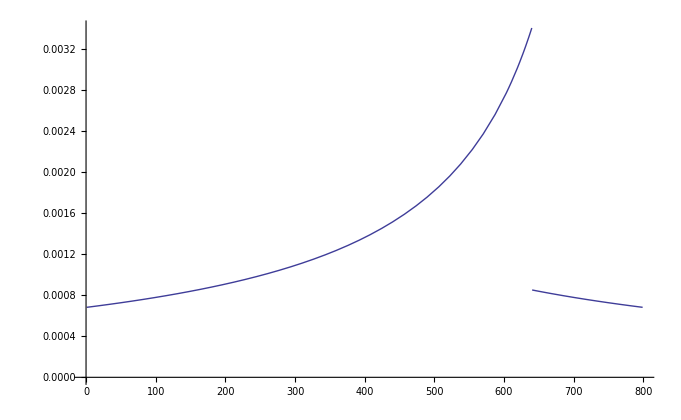

```mathematica
With[{n=800},Plot[postmxUnsimplified[80/100,i,n],{i,1,n-1},AxesOrigin->{0,0}]]
```

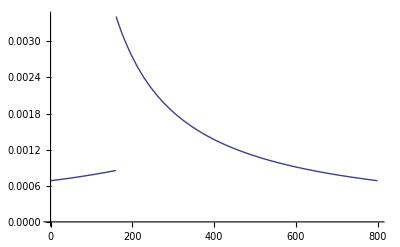

```mathematica
With[{n=800},Plot[postmxUnsimplified[20/100,i,n],{i,1,n-1},AxesOrigin->{0,0}]]
```

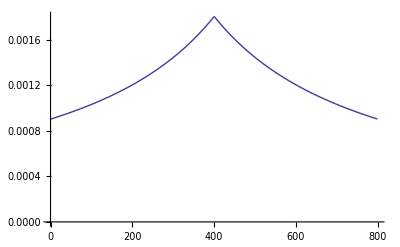

```mathematica
With[{n=800},Plot[postmxUnsimplified[50/100,i,n],{i,1,n-1},AxesOrigin->{0,0}]]
```

What does the posterior look like for different observations

```mathematica
With[{n=800},Plot3D[postmxUnsimplified[x,i,n],{i,1,n-1},{x,0,1}]]
```

-Graphics3D-

It looks like the most probable boundary is always at the observation.

```mathematica
N[Maximize[{postmxUnsimplified[#,i,80],i≤79},i]&/@(Range[80]/80)]
```

{{0.252166,{i→1.}},{0.143742,{i→2.}},{0.105548,{i→3.}},{0.0855792,{i→4.}},{0.0731368,{i→5.}},{0.0645632,{i→6.}},{0.0582546,{i→7.}},{0.0533919,{i→8.}},{0.0495114,{i→9.}},{0.0463298,{i→10.}},{0.0436638,{i→11.}},{0.0413895,{i→12.}},{0.0394195,{i→13.}},{0.0376908,{i→14.}},{0.0361565,{i→15.}},{0.0347809,{i→16.}},{0.0335365,{i→17.}},{0.0324017,{i→18.}},{0.0313591,{i→19.}},{0.0303949,{i→20.}},{0.0294974,{i→21.}},{0.0286575,{i→22.}},{0.0278671,{i→23.}},{0.0271199,{i→24.}},{0.0264101,{i→25.}},{0.0257332,{i→26.}},{0.0250851,{i→27.}},{0.0244623,{i→28.}},{0.0238619,{i→29.}},{0.0232813,{i→30.}},{0.0227183,{i→31.}},{0.022171,{i→32.}},{0.0216377,{i→33.}},{0.021117,{i→34.}},{0.0206076,{i→35.}},{0.0201084,{i→36.}},{0.0196185,{i→37.}},{0.019137,{i→38.}},{0.0186633,{i→39.}},{0.0181967,{i→40.}},{0.0186463,{i→41.}},{0.0191022,{i→42.}},{0.0195649,{i→43.}},{0.0200352,{i→44.}},{0.0205137,{i→45.}},{0.0210013,{i→46.}},{0.0214991,{i→47.}},{0.0220083,{i→48.}},{0.0225303,{i→49.}},{0.0230665,{i→50.}},{0.0236187,{i→51.}},{0.0241892,{i→52.}},{0.0247801,{i→53.}},{0.0253944,{i→54.}},{0.0260351,{i→55.}},{0.026706,{i→56.}},{0.0274115,{i→57.}},{0.0281566,{i→58.}},{0.0289475,{i→59.}},{0.0297912,{i→60.}},{0.0306964,{i→61.}},{0.0316734,{i→62.}},{0.032735,{i→63.}},{0.0338967,{i→64.}},{0.0351781,{i→65.}},{0.0366038,{i→66.}},{0.0382056,{i→67.}},{0.0400252,{i→68.}},{0.042118,{i→69.}},{0.0445602,{i→70.}},{0.0474594,{i→71.}},{0.0509727,{i→72.}},{0.0553399,{i→73.}},{0.0609473,{i→74.}},{0.0684634,{i→75.}},{0.0791612,{i→76.}},{0.0958279,{i→77.}},{0.126083,{i→78.}},{0.201899,{i→79.}},{0.201899,{i→79.}}}

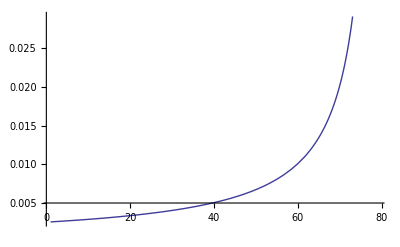

```mathematica
Plot[postmxUnsimplified[1,i,80],{i,1,79}]
```